```mathematica
A=RotationMatrix[2π/3];
MatrixForm[A]
```

(-1/2 | -(√3)/2
(√3)/2 | -1/2)

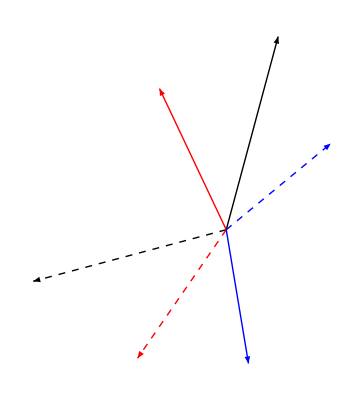

```mathematica
v1={7,26};v2={-9,19};v3={3,-18};
Graphics[{
Arrow[{{0,0},v1}],Dashed,Arrow[A.#&/@{{0,0},v1}],
Red,Dashing[{}],
Arrow[{{0,0},v2}],Dashed,Arrow[A.#&/@{{0,0},v2}],
Blue,Dashing[{}],
Arrow[{{0,0},v3}],Dashed,Arrow[A.#&/@{{0,0},v3}]
}]
```